```mathematica
(* Discrete-time geometric growth *)
(* Note that the symbol 'N' is protected, so use 'n' *)
sol=RSolve[{n[t+1]==λ n[t],n[0]==1},n[t],t]
```

{{n[t]→λ^t}}

```mathematica
dat=Table[{t,n[t]/.sol[[1]]/.λ->2},{t,0,10}]
```

{{0,1},{1,2},{2,4},{3,8},{4,16},{5,32},{6,64},{7,128},{8,256},{9,512},{10,1024}}

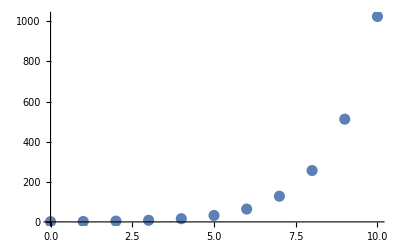

```mathematica
ListPlot[dat,{Joined->False,PlotStyle->{PointSize[0.02]}}]
```

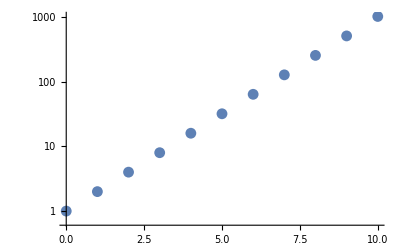

```mathematica
ListLogPlot[dat]
```

```mathematica
dat2=Table[{t,n[t]/.sol[[1]]/.λ->1.8},{t,0,10}]
```

{{0,1},{1,1.8},{2,3.24},{3,5.832},{4,10.4976},{5,18.8957},{6,34.0122},{7,61.222},{8,110.2},{9,198.359},{10,357.047}}

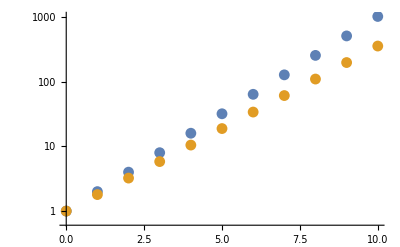

```mathematica
ListLogPlot[{dat,dat2}]
```

```mathematica
dat//MatrixForm
delN=Ratios[dat[[All,2]]]
```

(0 | 1
1 | 2
2 | 4
3 | 8
4 | 16
5 | 32
6 | 64
7 | 128
8 | 256
9 | 512
10 | 1024)

{2,2,2,2,2,2,2,2,2,2}

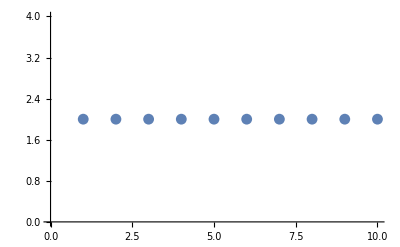

```mathematica
ListPlot[Thread[delN,dat[[1;;10,2]]],{Joined->False}]
```

```mathematica
sol2=RSolve[{n[t+1]==λ n[t],n[0]==1000},n[t],t];
dat3=Table[{t,n[t]/.sol2[[1]]/.λ->0.8},{t,0,100}];dat3//MatrixForm
```

(0 | 1000
1 | 800.
2 | 640.
3 | 512.
4 | 409.6
5 | 327.68
6 | 262.144
7 | 209.715
8 | 167.772
9 | 134.218
10 | 107.374
11 | 85.8993
12 | 68.7195
13 | 54.9756
14 | 43.9805
15 | 35.1844
16 | 28.1475
17 | 22.518
18 | 18.0144
19 | 14.4115
20 | 11.5292
21 | 9.22337
22 | 7.3787
23 | 5.90296
24 | 4.72237
25 | 3.77789
26 | 3.02231
27 | 2.41785
28 | 1.93428
29 | 1.54743
30 | 1.23794
31 | 0.990352
32 | 0.792282
33 | 0.633825
34 | 0.50706
35 | 0.405648
36 | 0.324519
37 | 0.259615
38 | 0.207692
39 | 0.166153
40 | 0.132923
41 | 0.106338
42 | 0.0850706
43 | 0.0680565
44 | 0.0544452
45 | 0.0435561
46 | 0.0348449
47 | 0.0278759
48 | 0.0223007
49 | 0.0178406
50 | 0.0142725
51 | 0.011418
52 | 0.00913439
53 | 0.00730751
54 | 0.00584601
55 | 0.00467681
56 | 0.00374144
57 | 0.00299316
58 | 0.00239452
59 | 0.00191562
60 | 0.0015325
61 | 0.001226
62 | 0.000980797
63 | 0.000784638
64 | 0.00062771
65 | 0.000502168
66 | 0.000401735
67 | 0.000321388
68 | 0.00025711
69 | 0.000205688
70 | 0.00016455
71 | 0.00013164
72 | 0.000105312
73 | 0.0000842498
74 | 0.0000673999
75 | 0.0000539199
76 | 0.0000431359
77 | 0.0000345087
78 | 0.000027607
79 | 0.0000220856
80 | 0.0000176685
81 | 0.0000141348
82 | 0.0000113078
83 | 9.04626×10^-6
84 | 7.23701×10^-6
85 | 5.7896×10^-6
86 | 4.63168×10^-6
87 | 3.70535×10^-6
88 | 2.96428×10^-6
89 | 2.37142×10^-6
90 | 1.89714×10^-6
91 | 1.51771×10^-6
92 | 1.21417×10^-6
93 | 9.71334×10^-7
94 | 7.77068×10^-7
95 | 6.21654×10^-7
96 | 4.97323×10^-7
97 | 3.97859×10^-7
98 | 3.18287×10^-7
99 | 2.54629×10^-7
100 | 2.03704×10^-7)

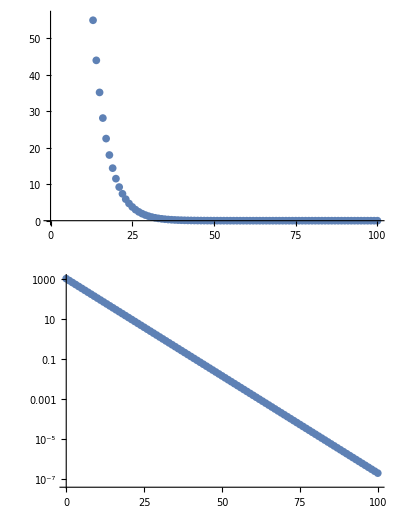

```mathematica
QE=1/1000;
GraphicsGrid[{{ListPlot[dat3]},{ListLogPlot[dat3]}}]
```